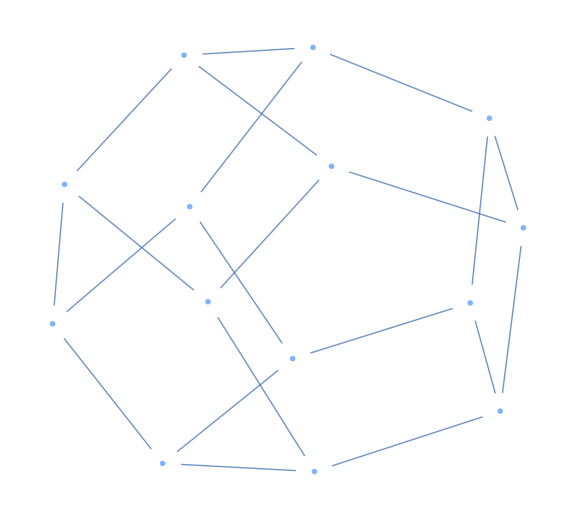

```mathematica
(* Load package *)
Needs["TriangleLink`"];
(* Construct delaunay triangulation *)
delTri=Sort[TriangleDelaunay[pts][[2]]];
(* Set up flip graph variables *)
triangulations={delTri};
sortedTriangulations={Sort[Sort/@delTri]};
edges={};

(* Queue tracks triangulations that still need to be explored *)
(* Start with just the Delaunay triangulation *)
queue={1};

While[Length[queue]>0,
(* Pop the queue by removing and saving the first element *)
currIndex=First[queue];
currTriangulation=triangulations[[currIndex]];
queue=Rest[queue];

(* Find the convex quadrilaterals of the current triangulation *)

(* Loop through each triangle T1 except for the last *)
For[i=1,i<Length[currTriangulation],++i,
(* Loop through each triangle T2 that comes after T1 *)
For[j=i+1,j<=Length[currTriangulation],++j,
(* Get the union of the points that describe T1 and T2 *)
comb=Union@@currTriangulation[[{i,j}]];

(* If the union has 4 points, then T1 and T2 share an edge and their union forms a quadrilateral *)
If[Length[comb]==4,
(* Find the index of the point in the union that has the lowest y-value (right x-value in ties) - which becomes the anchor point *)
minIndex=Sort[MinimalBy[{1,2,3,4},pts[[comb[[#]],2]]&],#1[[1]]>#2[[1]]&][[1]];

(* Swap the first point and the anchor point *)
comb[[{1,minIndex}]]=comb[[{minIndex,1}]];
(* Sort the other three points by their angle to the anchor point from the right horizontal, in descending order *)
comb[[2;;]]=Sort[comb[[2;;]],PositivelyOrientedPoints[{pts[[#1]],pts[[comb[[1]]]],pts[[#2]]}]&];

(* Check if the quadrilateral is convex *)
If[ConvexRegionQ[MeshRegion[pts,Polygon[comb]]],
newTriangulation=currTriangulation;

(* Find the two shared points of the two triangles *)
shared=Intersection@@currTriangulation[[{i,j}]];
(* Find the two unshared points of the two triangles *)
unshared=SymmetricDifference@@currTriangulation[[{i,j}]];

(* Create a new triangle consisting of the unshared points plus one of the shared *)
newT1=Append[unshared,shared[[1]]];
(* Rearrange the order of the points so that the triangle is described in counter clockwise order *)
If[PositivelyOrientedPoints[newT1],newT1=Reverse[newT1]];

(* Repeat for the other shared point *)
newT2=Append[unshared,shared[[2]]];
If[PositivelyOrientedPoints[newT2],newT2=Reverse[newT2]];

(* Replace the triangles of the convex quadrilateral with the new triangles to reflect the edge flip *)
newTriangulation[[{i,j}]]={newT1,newT2};
sortedNewTriangulation=Sort[Sort/@newTriangulation];

(* Verify if the new triangulation is new globally *)
If[!MemberQ[sortedTriangulations,sortedNewTriangulation],
(* Triangulation is new, add it *)
triangulations=Append[triangulations,newTriangulation];
sortedTriangulations=Append[sortedTriangulations,sortedNewTriangulation];

(* Record connection between the current and the new triangulation *)
newIndex=Length[triangulations];
edges=Append[edges,{currIndex,newIndex}];

(* Push index of new triangulation to the queue *)
queue=Append[queue,newIndex],

(* Trianglation is not new, check for edge and add it if not yet included *)
newIndex=Position[sortedTriangulations,sortedNewTriangulation][[1,1]];
newEdge=Sort[{currIndex,newIndex}];
If[!MemberQ[edges,newEdge],edges=Append[edges,newEdge]]
];
];
];
];
];
];

(* Generate mesh regions from each triangulation of the flip graph to use as vertices *)
vertexShapes={};
For[i=1,i<=Length[triangulations],++i,
vertexShapes=Append[vertexShapes,i->MeshRegion[pts,Polygon[triangulations[[i]]]]];
];

(* Construct the flip graph visualization *)
Graph[edges,VertexShape->vertexShapes,VertexSize->Large,ImageSize->Large]
```

```mathematica
pts=RandomReal[10,{10,2}];
LocatorPane[Dynamic[pts],Graphics[{Blue,PointSize[0.03],Point[Dynamic[pts]]},Frame->True,PlotRange->{{0,10},{0,10}}],Appearance->None,LocatorAutoCreate->True]
```

```mathematica
Length[triangulations]
```

80

```mathematica
pts
```

{{6.18432,3.8194},{0.704242,1.22642},{7.30981,2.11511},{3.99367,7.17538},{2.27801,7.29076},{7.88679,6.7252},{9.6539,5.97078},{3.60766,3.64946},{6.47977,1.61968},{3.39668,3.84947}}